0.5-2.5 x

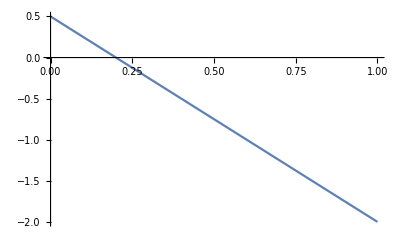

{{0.05,0.375},{0.1,0.25},{0.15,0.125},{0.2,0.}}

```mathematica
x0 = 0.2;
y0 = 0;
x1 = 0;
y1 =0.5;

sol =Solve[(y-y1)/(x-x1)==(y0-y1)/(x0-x1),y];
 Simplify[y/.sol[[1]]]

f[x_]:=0.5-2.5  *x;

Plot[f[x],{x,0,1}]
yoo=Range[4];

For[i=1,i<=4,i++,
xi=(x0-x1)*i/4;
yoo[[i]]={xi,f[xi]};
]
yoo
Clear["Global`*"]
```

-0.5+2.5 x

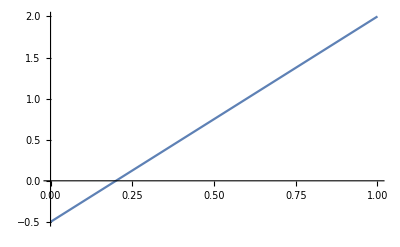

{{0.25,0.125},{0.3,0.25},{0.35,0.375},{0.4,0.5}}

```mathematica
x0 = 0.2;
y0 = 0;
x1 = 0.4;
y1 =0.5;

sol =Solve[(y-y1)/(x-x1)==(y0-y1)/(x0-x1),y];
 Simplify[y/.sol[[1]]]

f[x_]:=-0.5+2.5 x;

Plot[f[x],{x,0,1}]
yoo=Range[4];

For[i=1,i<=4,i++,
If[x0>x1,xtemp=x0;x0=x1;x1=xtemp];
xi=(x1-x0)*i/4+x0;
yoo[[i]]={xi,f[xi]};
]
yoo
Clear["Global`*"]
```

1.5-2.5 x

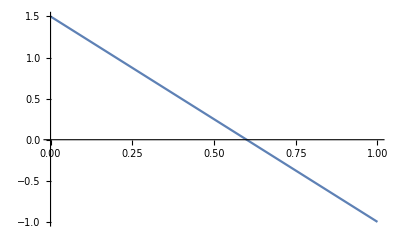

{{0.45,0.375},{0.5,0.25},{0.55,0.125},{0.6,0.}}

```mathematica
x0 = 0.6;
y0 = 0;
x1 = 0.4;
y1 =0.5;

sol =Solve[(y-y1)/(x-x1)==(y0-y1)/(x0-x1),y];
 Simplify[y/.sol[[1]]]

f[x_]:=1.5000000000000002-2.5000000000000004  x;

Plot[f[x],{x,0,1}]
yoo=Range[4];

For[i=1,i<=4,i++,
If[x0>x1,xtemp=x0;x0=x1;x1=xtemp];
xi=(x1-x0)*i/4+x0;
yoo[[i]]={xi,f[xi]};
]
yoo
Clear["Global`*"]
```

-1.5+2.5 x

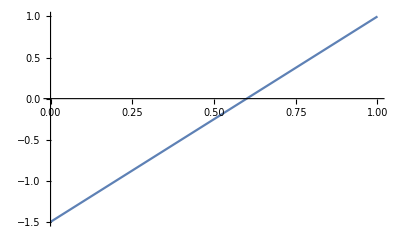

{{0.65,0.125},{0.7,0.25},{0.75,0.375},{0.8,0.5}}

```mathematica
x0 = 0.6;
y0 = 0;
x1 = 0.8;
y1 =0.5;

sol =Solve[(y-y1)/(x-x1)==(y0-y1)/(x0-x1),y];
 Simplify[y/.sol[[1]]]

f[x_]:=-1.4999999999999993+2.499999999999999  x;

Plot[f[x],{x,0,1}]
yoo=Range[4];

For[i=1,i<=4,i++,
If[x0>x1,xtemp=x0;x0=x1;x1=xtemp];
xi=(x1-x0)*i/4+x0;
yoo[[i]]={xi,f[xi]};
]
yoo
Clear["Global`*"]
```

```mathematica
Data = Join[{{0.05,0.375},{0.1,0.25},{0.15,0.125},{0.2,0.}},{{0.25,0.125},{0.3,0.25},{0.35,0.375},{0.4,0.5}},{{0.45,0.375},{0.5,0.25},{0.55,0.125},{0.6,0.}},{{0.65,0.125},{0.7,0.25},{0.75,0.375},{0.8,0.5}}];
Data1=Range[Length[Data]];
For[i =1, i≤Length[Data],i++,
Data1[[i]] = {Sqrt[Data[[i,1]]^2+Data[[i,2]]^2],N[ArcTan[Data[[i,2]]/Data[[i,1]]]/Degree]};
]
Data1
Clear["Global`*"]
```

{{0.378319,82.4054},{0.269258,68.1986},{0.195256,39.8056},{0.2,0.},{0.279508,26.5651},{0.390512,39.8056},{0.512957,46.9749},{0.640312,51.3402},{0.585769,39.8056},{0.559017,26.5651},{0.564026,12.8043},{0.6,0.},{0.66191,10.8855},{0.743303,19.6538},{0.838525,26.5651},{0.943398,32.0054}}